# Atom-field interactions (fully quantum)

## Atom-field interaction (quantum model two level atom and single mode field)

Multiple mode field and two level atom Hamiltonian:

```mathematica
setFockSize[11]
```

Two level atom

```mathematica
atom =QuantumBasis[QuditBasis[{"a","b"}]]
```

QuantumBasis[…]

```mathematica
HAtom = QuantumOperator[DiagonalMatrix[{Ea,Eb}],atom]
```

Eaaa+Ebbb

Hamiltonian considering only a single mode field and a two level atom (and using Rotating Wave Approximation in the interaction term)
also called Jaynes-Cummings Hamiltonian :

ℋ_0 =ℏνa^†a +1/2 ℏωσ_z
ℋ_1= ℏ g (σ_+a+ a^†σ_-)

```mathematica
H0 = h ν (QuantumTensorProduct[QuantumOperator["I",atom],numberOp ])+ 1/2 h ω QuantumTensorProduct[QuantumOperator["Z",atom],QuantumOperator["I"[fockBasis["Dimension"]]]]
```

QuantumOperator[…]

```mathematica
σplus =  QuantumOperator[{{0,1},{0,0}},atom]
```

QuantumOperator[…]

```mathematica
H1 = h g (QuantumTensorProduct[σplus,a]+QuantumTensorProduct[σplus["Dagger"],a["Dagger"]])
```

QuantumOperator[…]

Interaction picture Hamiltonian:

```mathematica
U = QuantumEvolve[H0/h,None,t]
```

ⅇ^(-1/2 ⅈ t ω)a0a0+ⅇ^(-ⅈ t ν-(ⅈ t ω)/2)a1a1+ⅇ^(-2 ⅈ t ν-(ⅈ t ω)/2)a2a2+ⅇ^(-3 ⅈ t ν-(ⅈ t ω)/2)a3a3+ⅇ^(-4 ⅈ t ν-(ⅈ t ω)/2)a4a4+ⅇ^(-5 ⅈ t ν-(ⅈ t ω)/2)a5a5+ⅇ^(-6 ⅈ t ν-(ⅈ t ω)/2)a6a6+ⅇ^(-7 ⅈ t ν-(ⅈ t ω)/2)a7a7+ⅇ^(-8 ⅈ t ν-(ⅈ t ω)/2)a8a8+ⅇ^(-9 ⅈ t ν-(ⅈ t ω)/2)a9a9+ⅇ^(-10 ⅈ t ν-(ⅈ t ω)/2)a10a10+ⅇ^((ⅈ t ω)/2)b0b0+ⅇ^(-ⅈ t ν+(ⅈ t ω)/2)b1b1+ⅇ^(-2 ⅈ t ν+(ⅈ t ω)/2)b2b2+ⅇ^(-3 ⅈ t ν+(ⅈ t ω)/2)b3b3+ⅇ^(-4 ⅈ t ν+(ⅈ t ω)/2)b4b4+ⅇ^(-5 ⅈ t ν+(ⅈ t ω)/2)b5b5+ⅇ^(-6 ⅈ t ν+(ⅈ t ω)/2)b6b6+ⅇ^(-7 ⅈ t ν+(ⅈ t ω)/2)b7b7+ⅇ^(-8 ⅈ t ν+(ⅈ t ω)/2)b8b8+ⅇ^(-9 ⅈ t ν+(ⅈ t ω)/2)b9b9+ⅇ^(-10 ⅈ t ν+(ⅈ t ω)/2)b10b10

```mathematica
HInteract = FullSimplify[U["Dagger"]@ H1 @ U,Element[{t,ω, h,ν},Reals]]
```

ⅇ^(-ⅈ t (ν-ω)) g ha0b1+√2 ⅇ^(-ⅈ t (ν-ω)) g ha1b2+√3 ⅇ^(-ⅈ t (ν-ω)) g ha2b3+2 ⅇ^(-ⅈ t (ν-ω)) g ha3b4+√5 ⅇ^(-ⅈ t (ν-ω)) g ha4b5+√6 ⅇ^(-ⅈ t (ν-ω)) g ha5b6+√7 ⅇ^(-ⅈ t (ν-ω)) g ha6b7+2 √2 ⅇ^(-ⅈ t (ν-ω)) g ha7b8+3 ⅇ^(-ⅈ t (ν-ω)) g ha8b9+√10 ⅇ^(-ⅈ t (ν-ω)) g ha9b10+ⅇ^(ⅈ t (ν-ω)) g hb1a0+√2 ⅇ^(ⅈ t (ν-ω)) g hb2a1+√3 ⅇ^(ⅈ t (ν-ω)) g hb3a2+2 ⅇ^(ⅈ t (ν-ω)) g hb4a3+√5 ⅇ^(ⅈ t (ν-ω)) g hb5a4+√6 ⅇ^(ⅈ t (ν-ω)) g hb6a5+√7 ⅇ^(ⅈ t (ν-ω)) g hb7a6+2 √2 ⅇ^(ⅈ t (ν-ω)) g hb8a7+3 ⅇ^(ⅈ t (ν-ω)) g hb9a8+√10 ⅇ^(ⅈ t (ν-ω)) g hb10a9

```mathematica
-Graphics--Graphics-
```

```mathematica
HInteract - h g (QuantumTensorProduct[σplus,a]Exp[t I  (ω-ν)]+QuantumTensorProduct[σplus["Dagger"],a["Dagger"]]Exp[-t I(ω-ν)])//Simplify
```

0

#### Differential equation method

Solving  ⅈ ℏ  (ⅆ |ψ⟩)/ⅆt = H_int |ψ⟩

```mathematica
atomField = QuantumBasis[{atom,fockBasis}];
```

```mathematica
generalState = QuantumState[Table[Subscript[c,x,y][t],{x,{"a","b"}},{y,0,fockBasis["Dimension"]-1}]//Flatten,atomField]
```

c_(a,0)(t)a0+c_(a,1)(t)a1+c_(a,2)(t)a2+c_(a,3)(t)a3+c_(a,4)(t)a4+c_(a,5)(t)a5+c_(a,6)(t)a6+c_(a,7)(t)a7+c_(a,8)(t)a8+c_(a,9)(t)a9+c_(a,10)(t)a10+c_(b,0)(t)b0+c_(b,1)(t)b1+c_(b,2)(t)b2+c_(b,3)(t)b3+c_(b,4)(t)b4+c_(b,5)(t)b5+c_(b,6)(t)b6+c_(b,7)(t)b7+c_(b,8)(t)b8+c_(b,9)(t)b9+c_(b,10)(t)b10

Get equations for c_(a n)(t), c_(b n)(t)

```mathematica
D[generalState,t]
```

c_(a,0)'(t)a0+c_(a,1)'(t)a1+c_(a,2)'(t)a2+c_(a,3)'(t)a3+c_(a,4)'(t)a4+c_(a,5)'(t)a5+c_(a,6)'(t)a6+c_(a,7)'(t)a7+c_(a,8)'(t)a8+c_(a,9)'(t)a9+c_(a,10)'(t)a10+c_(b,0)'(t)b0+c_(b,1)'(t)b1+c_(b,2)'(t)b2+c_(b,3)'(t)b3+c_(b,4)'(t)b4+c_(b,5)'(t)b5+c_(b,6)'(t)b6+c_(b,7)'(t)b7+c_(b,8)'(t)b8+c_(b,9)'(t)b9+c_(b,10)'(t)b10

```mathematica
Clear[solveCoeffEquations]
```

```mathematica
CoeffEquations[n_Integer/;n>=0]:= With[{Hi =-I/h HInteract @ generalState, baseSize = fockBasis["Dimension"]},
{(atomField["BasisStates"][[n+1]]["Dagger"] @ D[generalState,t])["Scalar"] == 
(atomField["BasisStates"][[n+1]]["Dagger"] @ Hi)["Scalar"],(atomField["BasisStates"][[baseSize+n+2]]["Dagger"] @ D[generalState,t])["Scalar"] == (atomField["BasisStates"][[baseSize+n+2]]["Dagger"] @ Hi)["Scalar"]}]
```

```mathematica
CoeffEquations[5]//Column
```

c_(a,5)'[t]==-ⅈ √6 ⅇ^(-ⅈ t (ν-ω)) g c_(b,6)[t]
c_(b,6)'[t]==-ⅈ √6 ⅇ^(ⅈ t (ν-ω)) g c_(a,5)[t]

ⅆ/dt c_(a,n) = - ⅈ g √(n + 1) e^ⅈΔt c_(b, n+1)
ⅆ/dt c_(b, n+1) = -ⅈ g √(n+1) e^(- ⅈΔt)c_(a, n)

Solving if initially c_(a,n)(0) = c_n and c_(b, n+1)(0) = 0 (initial atom excited state |a⟩)

```mathematica
Table[FullSimplify[DSolve[Join[CoeffEquations[n],{Subscript[c,"a",n][0] == c,Subscript[c,"b",n+1][0]==0}],{Subscript[c,"a",n][t],Subscript[c,"b",n+1][t]},t]//ComplexExpand,Element[{t,ω, h,ν,g},Reals] && g>0],{n,0,8}] //Column
```

{{c_(a,0)[t]→c ⅇ^(-1/2 ⅈ t (ν-ω)) (Cos[1/2 t √(4 g^2+(ν-ω)^2)]+(ⅈ (ν-ω) Sin[1/2 t √(4 g^2+(ν-ω)^2)])/(√(4 g^2+(ν-ω)^2))),c_(b,1)[t]→-(2 ⅈ c ⅇ^(1/2 ⅈ t (ν-ω)) g Sin[1/2 t √(4 g^2+(ν-ω)^2)])/(√(4 g^2+(ν-ω)^2))}}
{{c_(a,1)[t]→c ⅇ^(-1/2 ⅈ t (ν-ω)) (Cos[1/2 t √(8 g^2+(ν-ω)^2)]+(ⅈ (ν-ω) Sin[1/2 t √(8 g^2+(ν-ω)^2)])/(√(8 g^2+(ν-ω)^2))),c_(b,2)[t]→-(2 ⅈ √2 c ⅇ^(1/2 ⅈ t (ν-ω)) g Sin[1/2 t √(8 g^2+(ν-ω)^2)])/(√(8 g^2+(ν-ω)^2))}}
{{c_(a,2)[t]→c ⅇ^(-1/2 ⅈ t (ν-ω)) (Cos[1/2 t √(12 g^2+(ν-ω)^2)]+(ⅈ (ν-ω) Sin[1/2 t √(12 g^2+(ν-ω)^2)])/(√(12 g^2+(ν-ω)^2))),c_(b,3)[t]→-(2 ⅈ √3 c ⅇ^(1/2 ⅈ t (ν-ω)) g Sin[1/2 t √(12 g^2+(ν-ω)^2)])/(√(12 g^2+(ν-ω)^2))}}
{{c_(a,3)[t]→c ⅇ^(-1/2 ⅈ t (ν-ω)) (Cos[1/2 t √(16 g^2+(ν-ω)^2)]+(ⅈ (ν-ω) Sin[1/2 t √(16 g^2+(ν-ω)^2)])/(√(16 g^2+(ν-ω)^2))),c_(b,4)[t]→-(4 ⅈ c ⅇ^(1/2 ⅈ t (ν-ω)) g Sin[1/2 t √(16 g^2+(ν-ω)^2)])/(√(16 g^2+(ν-ω)^2))}}
{{c_(a,4)[t]→c ⅇ^(-1/2 ⅈ t (ν-ω)) (Cos[1/2 t √(20 g^2+(ν-ω)^2)]+(ⅈ (ν-ω) Sin[1/2 t √(20 g^2+(ν-ω)^2)])/(√(20 g^2+(ν-ω)^2))),c_(b,5)[t]→-(2 ⅈ √5 c ⅇ^(1/2 ⅈ t (ν-ω)) g Sin[1/2 t √(20 g^2+(ν-ω)^2)])/(√(20 g^2+(ν-ω)^2))}}
{{c_(a,5)[t]→c ⅇ^(-1/2 ⅈ t (ν-ω)) (Cos[1/2 t √(24 g^2+(ν-ω)^2)]+(ⅈ (ν-ω) Sin[1/2 t √(24 g^2+(ν-ω)^2)])/(√(24 g^2+(ν-ω)^2))),c_(b,6)[t]→-(2 ⅈ √6 c ⅇ^(1/2 ⅈ t (ν-ω)) g Sin[1/2 t √(24 g^2+(ν-ω)^2)])/(√(24 g^2+(ν-ω)^2))}}
{{c_(a,6)[t]→c ⅇ^(-1/2 ⅈ t (ν-ω)) (Cos[1/2 t √(28 g^2+(ν-ω)^2)]+(ⅈ (ν-ω) Sin[1/2 t √(28 g^2+(ν-ω)^2)])/(√(28 g^2+(ν-ω)^2))),c_(b,7)[t]→-(2 ⅈ √7 c ⅇ^(1/2 ⅈ t (ν-ω)) g Sin[1/2 t √(28 g^2+(ν-ω)^2)])/(√(28 g^2+(ν-ω)^2))}}
{{c_(a,7)[t]→c ⅇ^(-1/2 ⅈ t (ν-ω)) (Cos[1/2 t √(32 g^2+(ν-ω)^2)]+(ⅈ (ν-ω) Sin[1/2 t √(32 g^2+(ν-ω)^2)])/(√(32 g^2+(ν-ω)^2))),c_(b,8)[t]→-(4 ⅈ √2 c ⅇ^(1/2 ⅈ t (ν-ω)) g Sin[1/2 t √(32 g^2+(ν-ω)^2)])/(√(32 g^2+(ν-ω)^2))}}
{{c_(a,8)[t]→c ⅇ^(-1/2 ⅈ t (ν-ω)) (Cos[1/2 t √(36 g^2+(ν-ω)^2)]+(ⅈ (ν-ω) Sin[1/2 t √(36 g^2+(ν-ω)^2)])/(√(36 g^2+(ν-ω)^2))),c_(b,9)[t]→-(6 ⅈ c ⅇ^(1/2 ⅈ t (ν-ω)) g Sin[1/2 t √(36 g^2+(ν-ω)^2)])/(√(36 g^2+(ν-ω)^2))}}

Generalizing the result:

```mathematica
caN[c0_,n_]:= Function[t,c0 ⅇ^(-1/2 ⅈ t (ν-ω)) (Cos[1/2 t √(4 g^2(n+1)+(ν-ω)^2)]+(ⅈ (ν-ω) Sin[1/2 t √(4 g^2(n+1)+(ν-ω)^2)])/(√(4 g^2(n+1)+(ν-ω)^2)))]
cbN[c0_,n_]:= Function[t,-(2 ⅈ √n c0 ⅇ^(1/2 ⅈ t (ν-ω)) g Sin[1/2 t √(4 g^2 n+(ν-ω)^2)])/(√(4 g^2 n+(ν-ω)^2))]
```

Probability p(n) of finding n photons at time t:   p(n) =| c_(a,n)(t)|^2+ | c_(b,n)(t)|^2 
Computing the p(n) distribution with an initial coherent state with ⟨n⟩ = 25, and with parameters gt = 1, Δ = 0 (ν = ω)
⟨n⟩ = 25 corresponds to |α| = 5. A safe choice for the Fock basis size is |α|^2+3|α| to include the tails of the Poisson distribution

```mathematica
αmod = 5;
```

```mathematica
setFockSize[αmod^2 + 3 αmod]; atomField = QuantumBasis[{atom,fockBasis}];
```

```mathematica
generalState = QuantumState[Table[Subscript[c,x,y][t],{x,{"a","b"}},{y,0,fockBasis["Dimension"]-1}]//Flatten,atomField]
```

c_(a,0)(t)a0+c_(a,1)(t)a1+c_(a,2)(t)a2+c_(a,3)(t)a3+c_(a,4)(t)a4+c_(a,5)(t)a5+c_(a,6)(t)a6+c_(a,7)(t)a7+c_(a,8)(t)a8+c_(a,9)(t)a9+c_(a,10)(t)a10+c_(a,11)(t)a11+c_(a,12)(t)a12+c_(a,13)(t)a13+c_(a,14)(t)a14+c_(a,15)(t)a15+c_(a,16)(t)a16+c_(a,17)(t)a17+c_(a,18)(t)a18+c_(a,19)(t)a19+c_(a,20)(t)a20+c_(a,21)(t)a21+c_(a,22)(t)a22+c_(a,23)(t)a23+c_(a,24)(t)a24+c_(a,25)(t)a25+c_(a,26)(t)a26+c_(a,27)(t)a27+c_(a,28)(t)a28+c_(a,29)(t)a29+c_(a,30)(t)a30+c_(a,31)(t)a31+c_(a,32)(t)a32+c_(a,33)(t)a33+c_(a,34)(t)a34+c_(a,35)(t)a35+c_(a,36)(t)a36+c_(a,37)(t)a37+c_(a,38)(t)a38+c_(a,39)(t)a39+c_(b,0)(t)b0+c_(b,1)(t)b1+c_(b,2)(t)b2+c_(b,3)(t)b3+c_(b,4)(t)b4+c_(b,5)(t)b5+c_(b,6)(t)b6+c_(b,7)(t)b7+c_(b,8)(t)b8+c_(b,9)(t)b9+c_(b,10)(t)b10+c_(b,11)(t)b11+c_(b,12)(t)b12+c_(b,13)(t)b13+c_(b,14)(t)b14+c_(b,15)(t)b15+c_(b,16)(t)b16+c_(b,17)(t)b17+c_(b,18)(t)b18+c_(b,19)(t)b19+c_(b,20)(t)b20+c_(b,21)(t)b21+c_(b,22)(t)b22+c_(b,23)(t)b23+c_(b,24)(t)b24+c_(b,25)(t)b25+c_(b,26)(t)b26+c_(b,27)(t)b27+c_(b,28)(t)b28+c_(b,29)(t)b29+c_(b,30)(t)b30+c_(b,31)(t)b31+c_(b,32)(t)b32+c_(b,33)(t)b33+c_(b,34)(t)b34+c_(b,35)(t)b35+c_(b,36)(t)b36+c_(b,37)(t)b37+c_(b,38)(t)b38+c_(b,39)(t)b39

Projecting the general state with a particular occupation number

```mathematica
QuantumState["2",fockBasis]["Dagger"]@generalState["Reverse"]
```

c_(a,2)(t)a+c_(b,2)(t)b

```mathematica
αcoh =αmod Exp[I RandomReal[{0,2Pi}]]
```

-3.24066+3.80764 ⅈ

```mathematica
measurePhoton =QuantumMeasurementOperator[numberOp]@coh[αcoh];
```

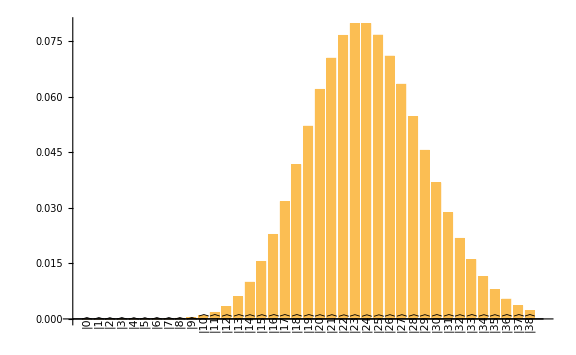

```mathematica
measurePhoton["ProbabilityPlot",ChartLabels->(Style[Rotate[StringForm["|``⟩",#],Pi/2],11]& /@Range[0,39]),ImageSize->Large]
```

```mathematica
{measurePhoton["Mean"],Abs[αcoh]^2}
```

{24.9435,25.}

Using the problem condition simplifications:

```mathematica
FullSimplify[Abs[(caN[cn,n][t]/. ν->ω)]^2+Abs[(cbN[cn1,n][t]/. ν->ω)]^2,
Element[{t,g},Reals]&& n>0]/. g-> 1/t
```

cn Conjugate[cn] Cos[√(1+n)]^2+cn1 Conjugate[cn1] Sin[√n]^2

```mathematica
pn = Function[{cn,cn1,n},Evaluate@ %]
```

Function[{cn,cn1,n},cn Conjugate[cn] Cos[√(1+n)]^2+cn1 Conjugate[cn1] Sin[√n]^2]

```mathematica
MapIndexed[pn[#1[[2]],#1[[1]],First[#2]]&,Partition[coh[αcoh]["AmplitudeList"],2,1]]//Re
```

{1.83402×10^-11,4.5219×10^-10,1.05276×10^-8,1.16432×10^-7,8.12646×10^-7,4.11767×10^-6,0.0000163445,0.0000532909,0.000147486,0.000355203,0.000759867,0.00147048,0.00261868,0.00436196,0.00689706,0.0104747,0.015391,0.0219287,0.0302388,0.0401907,0.0512538,0.0624797,0.0726241,0.0803904,0.0847227,0.0850507,0.0814091,0.0743985,0.065018,0.0544292,0.0437289,0.0337836,0.0251518,0.0180861,0.012592,0.00851052,0.00559934,0.00359655,0.00226181}

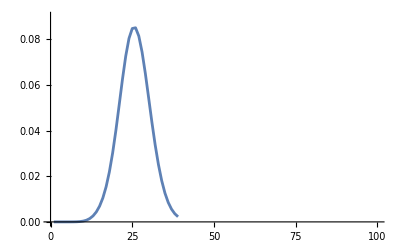

```mathematica
ListLinePlot[%,PlotRange->{{0,100},{0,0.09}}]
```

```mathematica
FullSimplify[Abs[(caN[cn,n][t]/. ν->ω)]^2-Abs[(cbN[cn1,n][t]/. ν->ω)]^2,
Element[{t,g},Reals]&& n>0]
```

cn Conjugate[cn] Cos[g √(1+n) t]^2-cn1 Conjugate[cn1] Sin[g √n t]^2

```mathematica
wn = Function[{cn,cn1,n},Evaluate @ %]
```

Function[{cn,cn1,n},cn Conjugate[cn] Cos[g √(1+n) t]^2-cn1 Conjugate[cn1] Sin[g √n t]^2]

Calculation of the population inversion W(t) under the same condition. For a coherent state there is a decay of Rabi oscillations and a revival at a later time which is a fully quantum behavior not explained by classical(and  semiclassical)models.

```mathematica
MapIndexed[wn[#1[[2]],#1[[1]],First[#2]]&,Partition[coh[αcoh]["AmplitudeList"],2,1]]/. g t->x //Total;
```

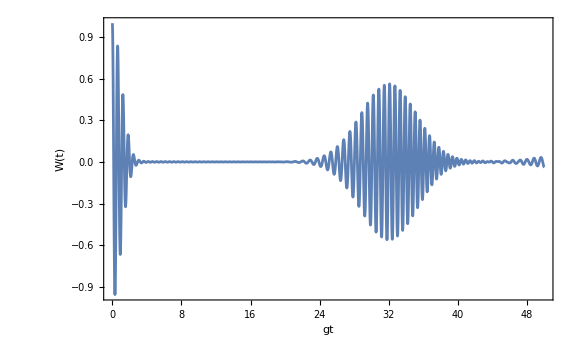

```mathematica
Plot[%,{x,0,50},PlotRange->Full,Frame->True,FrameLabel->(Style[#,18]&/@{"gt","W(t)"}),ImageSize->Large]
```

### Unitary operator method (QuantumEvolve)

```mathematica
setFockSize[11];atomField = QuantumBasis[{atom,fockBasis}];
```

```mathematica
H0 = h ν (QuantumTensorProduct[QuantumOperator["I",atom],numberOp ])+ 1/2 h ω QuantumTensorProduct[QuantumOperator["Z",atom],QuantumOperator["I"[fockBasis["Dimension"]]]]
```

QuantumOperator[…]

```mathematica
H1 = h g (QuantumTensorProduct[σplus,a]+QuantumTensorProduct[σplus["Dagger"],a["Dagger"]])
```

QuantumOperator[…]

```mathematica
U = QuantumEvolve[H0/h,None,t]
```

QuantumOperator[…]

```mathematica
HInteract = QuantumOperator[FullSimplify[U["Dagger"]@ H1 @ U,Element[{t,ω, h,ν},Reals]],"Parameters"->{ν,ω}]
```

QuantumOperator[…]

U(t) =  exp(-ⅈ H_int t /ℏ) where the H_int  considered at exact resonance Δ = 0 (ν = ω)

```mathematica
U2 = QuantumEvolve[HInteract[ν,ν]/h,None,t]
```

Cos[g t]a0a0-ⅈ Sin[g t]a0b1+Cos[√2 g t]a1a1-ⅈ Sin[√2 g t]a1b2+Cos[√3 g t]a2a2-ⅈ Sin[√3 g t]a2b3+Cos[2 g t]a3a3-ⅈ Sin[2 g t]a3b4+Cos[√5 g t]a4a4-ⅈ Sin[√5 g t]a4b5+Cos[√6 g t]a5a5-ⅈ Sin[√6 g t]a5b6+Cos[√7 g t]a6a6-ⅈ Sin[√7 g t]a6b7+Cos[2 √2 g t]a7a7-ⅈ Sin[2 √2 g t]a7b8+Cos[3 g t]a8a8-ⅈ Sin[3 g t]a8b9+Cos[√10 g t]a9a9-ⅈ Sin[√10 g t]a9b10+a10a10+b0b0-ⅈ Sin[g t]b1a0+Cos[g t]b1b1-ⅈ Sin[√2 g t]b2a1+Cos[√2 g t]b2b2-ⅈ Sin[√3 g t]b3a2+Cos[√3 g t]b3b3-ⅈ Sin[2 g t]b4a3+Cos[2 g t]b4b4-ⅈ Sin[√5 g t]b5a4+Cos[√5 g t]b5b5-ⅈ Sin[√6 g t]b6a5+Cos[√6 g t]b6b6-ⅈ Sin[√7 g t]b7a6+Cos[√7 g t]b7b7-ⅈ Sin[2 √2 g t]b8a7+Cos[2 √2 g t]b8b8-ⅈ Sin[3 g t]b9a8+Cos[3 g t]b9b9-ⅈ Sin[√10 g t]b10a9+Cos[√10 g t]b10b10

Also considering the case with initial excited atom |ψ(0) ⟩ = ∑_n c_n(0) |a,n⟩

```mathematica
ψ0=QuantumTensorProduct[QuantumState["0",atom],QuantumState[Table[Subscript[c,n],{n,0,fockBasis["Dimension"]-1}],fockBasis]]
```

c_0 a0+c_1 a1+c_2 a2+c_3 a3+c_4 a4+c_5 a5+c_6 a6+c_7 a7+c_8 a8+c_9 a9+c_10 a10

|ψ(t)⟩ =  U(t) |ψ(0)⟩

```mathematica
ψt = U2 @ ψ0
```

c_0 cos(g t)a0+c_1 cos(√2 g t)a1+c_2 cos(√3 g t)a2+c_3 cos(2 g t)a3+c_4 cos(√5 g t)a4+c_5 cos(√6 g t)a5+c_6 cos(√7 g t)a6+c_7 cos(2 √2 g t)a7+c_8 cos(3 g t)a8+c_9 cos(√10 g t)a9+c_10 a10-ⅈ c_0 sin(g t)b1-ⅈ c_1 sin(√2 g t)b2-ⅈ c_2 sin(√3 g t)b3-ⅈ c_3 sin(2 g t)b4-ⅈ c_4 sin(√5 g t)b5-ⅈ c_5 sin(√6 g t)b6-ⅈ c_6 sin(√7 g t)b7-ⅈ c_7 sin(2 √2 g t)b8-ⅈ c_8 sin(3 g t)b9-ⅈ c_9 sin(√10 g t)b10

Using a truncated basis  we only get a valid c_(a, n) for n = 0,1.. n_max-1

```mathematica
Transpose[{(QuantumState["0",atom]["Dagger"]@ ψt)["AmplitudeList"],Prepend[(QuantumState["1",atom]["Dagger"]@ ψt)["AmplitudeList"],0]}]//Grid
```

Cos[g t] c_0 | 0
Cos[√2 g t] c_1 | -ⅈ Sin[g t] c_0
Cos[√3 g t] c_2 | -ⅈ Sin[√2 g t] c_1
Cos[2 g t] c_3 | -ⅈ Sin[√3 g t] c_2
Cos[√5 g t] c_4 | -ⅈ Sin[2 g t] c_3
Cos[√6 g t] c_5 | -ⅈ Sin[√5 g t] c_4
Cos[√7 g t] c_6 | -ⅈ Sin[√6 g t] c_5
Cos[2 √2 g t] c_7 | -ⅈ Sin[√7 g t] c_6
Cos[3 g t] c_8 | -ⅈ Sin[2 √2 g t] c_7
Cos[√10 g t] c_9 | -ⅈ Sin[3 g t] c_8
c_10 | -ⅈ Sin[√10 g t] c_9

In agreement with the other method for the resonant case

```mathematica
Simplify[{caN[c,n][t]/. ν->ω, cbN[c,n+1][t]/. ν->ω},g >0]
```

{c Cos[g √(1+n) t],-ⅈ c Sin[g √(1+n) t]}

## Dressed states

```mathematica
setFockSize[12]; atomField = QuantumBasis[{atom,fockBasis}];
```

```mathematica
ℋfree =  h ν (QuantumTensorProduct[QuantumOperator["I",atom],numberOp ])+ 1/2 h ω QuantumTensorProduct[QuantumOperator["Z",atom],QuantumOperator["I"[fockBasis["Dimension"]]]] ;
```

```mathematica
ℋ =  h ν (QuantumTensorProduct[QuantumOperator["I",atom],numberOp ])+ 1/2 h ω QuantumTensorProduct[QuantumOperator["Z",atom],QuantumOperator["I"[fockBasis["Dimension"]]]] + h g (QuantumTensorProduct[σplus,a]+QuantumTensorProduct[σplus["Dagger"],a["Dagger"]]);
```

For a fixed n, the dynamics is determined by the product states |a⟩|n⟩, |b⟩|n+1⟩ ( or |a⟩|n-1⟩, |b⟩|n⟩ ). At near resonance(ν≃ ω) these pair of states  have almost the same energy . For a given n the bare states are defined:
|ψ_(0, n)⟩ = |a⟩ |n⟩
|ψ_(1, n)⟩  =  |b⟩ |n+1⟩

```mathematica
bareState[i_Integer,n_Integer/; 0<=n<= fockBasis["Dimension"]-1]:=QuantumTensorProduct[QuantumState[ToString[i],atom],QuantumState[SparseArray[n+i+1->1,fockBasis["Dimension"]],fockBasis]]
```

```mathematica
{bareState[0,10],bareState[1,9]}
```

{QuantumState[…],QuantumState[…]}

When we consider the free Hamiltonian the bare states are uncoupled and the energy difference is  related to the detuning   h Δ  (Δ = ν - ω)

```mathematica
Differences/@( Table[(ℋfree @ bareState[m,n])["Amplitude"]//First,{n,0,8},{m,0,1}])
```

{{h ν-h ω},{h ν-h ω},{h ν-h ω},{h ν-h ω},{h ν-h ω},{h ν-h ω},{h ν-h ω},{h ν-h ω},{h ν-h ω}}

The matrix elements for a given n of bare states, (ℋ^(n))_ij are:
(ℋ^(n))_00 = h[nν + 1/2ω]  
(ℋ^(n))_11 = h[(n+1)ν - 1/2ω] 
(ℋ^(n))_01 =(ℋ^(n))_10= hg √(n+1)

Matrix element calculations

```mathematica
nmax = fockBasis["Dimension"] - 2;
```

```mathematica
Table[(bareState[0,n]["Dagger"] @ ℋ @ bareState[0,n])["Scalar"],{n,0,nmax}]
```

{(h ω)/2,h ν+(h ω)/2,2 h ν+(h ω)/2,3 h ν+(h ω)/2,4 h ν+(h ω)/2,5 h ν+(h ω)/2,6 h ν+(h ω)/2,7 h ν+(h ω)/2,8 h ν+(h ω)/2,9 h ν+(h ω)/2,10 h ν+(h ω)/2}

```mathematica
Table[(bareState[1,n]["Dagger"] @ ℋ @ bareState[1,n])["Scalar"],{n,0,nmax}]
```

{h ν-(h ω)/2,2 h ν-(h ω)/2,3 h ν-(h ω)/2,4 h ν-(h ω)/2,5 h ν-(h ω)/2,6 h ν-(h ω)/2,7 h ν-(h ω)/2,8 h ν-(h ω)/2,9 h ν-(h ω)/2,10 h ν-(h ω)/2,11 h ν-(h ω)/2}

```mathematica
Table[(bareState[1,n]["Dagger"] @ ℋ @ bareState[0,n])["Scalar"],{n,0,nmax}]
```

{g h,√2 g h,√3 g h,2 g h,√5 g h,√6 g h,√7 g h,2 √2 g h,3 g h,√10 g h,√11 g h}

```mathematica
Table[(bareState[0,n]["Dagger"] @ ℋ @ bareState[1,n])["Scalar"],{n,0,nmax}]
```

{g h,√2 g h,√3 g h,2 g h,√5 g h,√6 g h,√7 g h,2 √2 g h,3 g h,√10 g h,√11 g h}

With those matrix elements we can generate a matrix that contains the dynamics (coupling because of the interaction term of the Hamiltonian) of a 2x2 subspace for a given n

```mathematica
dressedSubspace = QuantumOperator[{{h(n ν +1/2  ω),h g √(n+1)},{h g √(n+1), h((n+1) ν -1/2 ω)}}]
```

QuantumOperator[…]

```mathematica
ReplaceAll[#,{(ν-ω)->Δ}]& /@(dressedSubspace["Eigenvalues"])
```

{1/2 h (-√(4 g^2 (1+n)+Δ^2)+ν+2 n ν),1/2 h (√(4 g^2 (1+n)+Δ^2)+ν+2 n ν)}

With the interaction Hamiltonian there is an energy shift  hΩ_n(Δ) (when g = 0 there is no interaction and we recover the previous result) Ω_n(Δ) = √(4g^2(n+1) + Δ^2) (generalized Rabi frequency). The energy splitting of the states is also called AC Stark Shift

```mathematica
% //Differences //Simplify
```

{h √(4 g^2 (1+n)+Δ^2)}

The eigenstates associated with the energy eigenvalues have the following form:
|n, +⟩ =  cos(Φ_n/2)|ψ_(0, n)⟩  +  sin(Φ_n/2) |ψ_(1, n)⟩ 
|n, - ⟩ =  -sin(Φ_n/2)|ψ_(0, n)⟩  +  cos(Φ_n/2) |ψ_(1, n)⟩ 
such  Φ_n= tan^-1((2 g √(n+1))/Δ)    and where  sin(Φ_n/2) = (1/(√2)[(Ω_n-Δ)/Ω_n])^(1/2), cos(Φ_n/2) = (1/(√2)[(Ω_n+Δ)/Ω_n])^(1/2)

```mathematica
FullSimplify[(dressedSubspace["Eigenvectors"]//. {ν-ω->Δ,-ν+ω->-Δ,√(4 g^2 (1+n)+Δ^2)->Subscript[Ω, n]}) ,Element[{Subscript[Ω, n],g,n,Δ},Reals] && Subscript[Ω, n]>Δ>0 && n>0 && g>0]
```

{{-(Δ+Ω_n)/(√(4 g^2 (1+n)+Δ^2+2 Δ Ω_n+Ω_n^2)),2/(√(4+(Δ+Ω_n)^2/(g^2 (1+n))))},{(-Δ+Ω_n)/(√(4 g^2 (1+n)+Δ^2-2 Δ Ω_n+Ω_n^2)),2/(√(4+(Δ-Ω_n)^2/(g^2 (1+n))))}}

Eigenvectors find a different set of valid eigenvectors of the form {-cos, sin} and {sin, -cos}

```mathematica
FullSimplify[#/.{ 1/(g^2(n+1))->4/( Subscript[Ω, n]^2-Δ^2), 4 g^2(n+1)->Subscript[Ω, n]^2-Δ^2 },Subscript[Ω, n]>0 && Δ>0]& /@ % //Together
```

{{-(√((Δ+Ω_n)/Ω_n))/(√2),1/(√2 √(Ω_n/(-Δ+Ω_n)))},{(√((-Δ+Ω_n)/Ω_n))/(√2),(√((Δ+Ω_n)/Ω_n))/(√2)}}

This is the typical form in accordance with the literature

```mathematica
dressedEigenvectors = Map[{-#[[1]],#[[2]]}&,((#/. 1/(Sqrt[a_?NumericQ] Sqrt[b_]):>Sqrt[1/b]/Sqrt[a])& /@ % ) ]
```

{{(√((Δ+Ω_n)/Ω_n))/(√2),(√((-Δ+Ω_n)/Ω_n))/(√2)},{-(√((-Δ+Ω_n)/Ω_n))/(√2),(√((Δ+Ω_n)/Ω_n))/(√2)}}

When Δ = 0 the bare states are degenerate  h(ν-ω) = 0 but the splitting remains h Ω_n(0) = 2h g √(n+1)

```mathematica
dressedSubspace["Eigenvalues"]/. ν->ω //Differences//Simplify
```

{2 h √(g^2 (1+n))}

```mathematica
dressedEigenvectors /. Δ->0
```

{{1/(√2),1/(√2)},{-1/(√2),1/(√2)}}

In this limit the dressed states are related to the bare states as 
|n, +⟩ = 1/(√2)|a⟩|n⟩ + |b⟩|n+1⟩) , 
|n, -⟩ = 1/(√2)(-|a⟩|n⟩ + |b⟩|n+1⟩)

## Jaynes Cummings : density operator applied to thermal states

Field Basis:

```mathematica
setFockSize[40]
```

Atom Basis:

```mathematica
atom = QuantumBasis[QuditBasis[{"e","g"}]]
```

<|e→{1,0},g→{0,1}|>

Transition operators:

```mathematica
σplus =  QuantumOperator["JZ-",atom]
σminus = QuantumOperator["JZ+",atom]
```

eg

ge

Interaction picture Hamiltonian at resonance:

```mathematica
Hinteract=h λ  (QuantumTensorProduct[σplus,a]+QuantumTensorProduct[σminus,a["Dagger"]])
```

QuantumOperator[…]

Since H_I (t) is independent of time , we have a direct solution

```mathematica
U = Exp[-ⅈ Hinteract t /h];
```

We take the example of  an atom initially in the excited state and the field is in a thermal state with n^—=5

```mathematica
ρ0 = QuantumTensorProduct[QuantumState["0",atom]["MatrixState"],thermalState[5.,fockBasis["Dimension"]-1]]
```

QuantumState[…]

ρ(t) = U_I (t) ρ(0) U_I (t)^†

```mathematica
ρt  = QuantumCircuitOperator[{ρ0 ,U["Dagger"]}][]
```

QuantumState[…]

The atomic inversion is calculated W(t) = ρ_ee^A(t)-ρ_gg^A(t) = (2 ρ_ee)^A(t)-1 ,   after tracing the Fock states

```mathematica
rhoee =Simplify[QuantumPartialTrace[ρt,{2}]["Matrix"][[1,1]] /. t λ-> T,Element[T,Reals]];
```

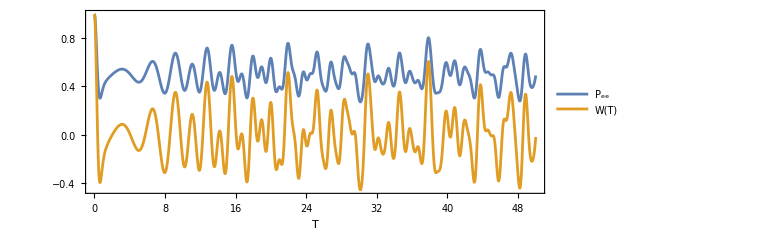

```mathematica
Plot[{rhoee,2rhoee-1},{T,0,50},Frame->True,FrameLabel->(Style[#,14]&)/@{"T"},ImageSize->Large,AspectRatio->0.4,PlotLegends->{"P_ee","W(T)"}]
```

This is a known behavior for this type of state see here

```mathematica
FullSimplify[QuantumPartialTrace[ρt,{2}]["Matrix"][[1,1]] /. t λ-> T,Element[T,Reals]]
```

0.5+0.166667 Cos[2 T]+0.0493827 Cos[4 T]+0.00650307 Cos[6 T]+0.00038061 Cos[8 T]+9.90053×10^-6 Cos[10 T]+1.1446×10^-7 Cos[12 T]+0.111111 Cos[2 √2 T]+0.00975461 Cos[4 √2 T]+0.00016916 Cos[6 √2 T]+5.79455×10^-7 Cos[8 √2 T]+0.0740741 Cos[2 √3 T]+0.00192684 Cos[4 √3 T]+4.40024×10^-6 Cos[6 √3 T]+0.0329218 Cos[2 √5 T]+0.0000751822 Cos[4 √5 T]+0.0219479 Cos[2 √6 T]+0.0000148508 Cos[4 √6 T]+0.0146319 Cos[2 √7 T]+2.93349×10^-6 Cos[4 √7 T]+0.00433538 Cos[2 √10 T]+0.00289025 Cos[2 √11 T]+0.00128456 Cos[2 √13 T]+0.000856372 Cos[2 √14 T]+0.000570915 Cos[2 √15 T]+0.00025374 Cos[2 √17 T]+0.000112773 Cos[2 √19 T]+0.0000501214 Cos[2 √21 T]+0.0000334143 Cos[2 √22 T]+0.0000222762 Cos[2 √23 T]+6.60035×10^-6 Cos[2 √26 T]+1.95566×10^-6 Cos[2 √29 T]+1.30377×10^-6 Cos[2 √30 T]+8.69183×10^-7 Cos[2 √31 T]+3.86303×10^-7 Cos[2 √33 T]+2.57536×10^-7 Cos[2 √34 T]+1.7169×10^-7 Cos[2 √35 T]+7.63068×10^-8 Cos[2 √37 T]+5.08712×10^-8 Cos[2 √38 T]+3.39141×10^-8 Cos[2 √39 T]

The theoretical solution for ρ_ee(t) = ∑_(n=0)^∞ |C_n|^2(cos(λ t √(n+1)))^2

```mathematica
(thermalState[5.,fockBasis["Dimension"]-1]["Probability"]//Values ) Table[Cos[T (√(n+1))]^2,{n,0,fockBasis["Dimension"]-1}]//TrigReduce//Total
```

0.5+0.166667 Cos[2 T]+0.0493827 Cos[4 T]+0.00650307 Cos[6 T]+0.00038061 Cos[8 T]+9.90053×10^-6 Cos[10 T]+1.1446×10^-7 Cos[12 T]+0.111111 Cos[2 √2 T]+0.00975461 Cos[4 √2 T]+0.00016916 Cos[6 √2 T]+5.79455×10^-7 Cos[8 √2 T]+0.0740741 Cos[2 √3 T]+0.00192684 Cos[4 √3 T]+4.40024×10^-6 Cos[6 √3 T]+0.0329218 Cos[2 √5 T]+0.0000751822 Cos[4 √5 T]+0.0219479 Cos[2 √6 T]+0.0000148508 Cos[4 √6 T]+0.0146319 Cos[2 √7 T]+2.93349×10^-6 Cos[4 √7 T]+0.00433538 Cos[2 √10 T]+2.26094×10^-8 Cos[4 √10 T]+0.00289026 Cos[2 √11 T]+0.00128456 Cos[2 √13 T]+0.000856372 Cos[2 √14 T]+0.000570915 Cos[2 √15 T]+0.00025374 Cos[2 √17 T]+0.000112773 Cos[2 √19 T]+0.0000501214 Cos[2 √21 T]+0.0000334143 Cos[2 √22 T]+0.0000222762 Cos[2 √23 T]+6.60036×10^-6 Cos[2 √26 T]+1.95566×10^-6 Cos[2 √29 T]+1.30377×10^-6 Cos[2 √30 T]+8.69183×10^-7 Cos[2 √31 T]+3.86303×10^-7 Cos[2 √33 T]+2.57536×10^-7 Cos[2 √34 T]+1.7169×10^-7 Cos[2 √35 T]+7.63068×10^-8 Cos[2 √37 T]+5.08712×10^-8 Cos[2 √38 T]+3.39142×10^-8 Cos[2 √39 T]

Slight error for considering a truncated Fock Basis

```mathematica
(% - %%)//Chop
```

2.26094×10^-8+1.5073×10^-8 Cos[2 T]+4.46606×10^-9 Cos[4 T]+5.88123×10^-10 Cos[6 T]+1.00486×10^-8 Cos[2 √2 T]+8.82185×10^-10 Cos[4 √2 T]+6.69909×10^-9 Cos[2 √3 T]+1.74259×10^-10 Cos[4 √3 T]+2.97737×10^-9 Cos[2 √5 T]+1.98492×10^-9 Cos[2 √6 T]+1.32328×10^-9 Cos[2 √7 T]+3.92082×10^-10 Cos[2 √10 T]+2.26094×10^-8 Cos[4 √10 T]+2.61388×10^-10 Cos[2 √11 T]+1.16172×10^-10 Cos[2 √13 T]